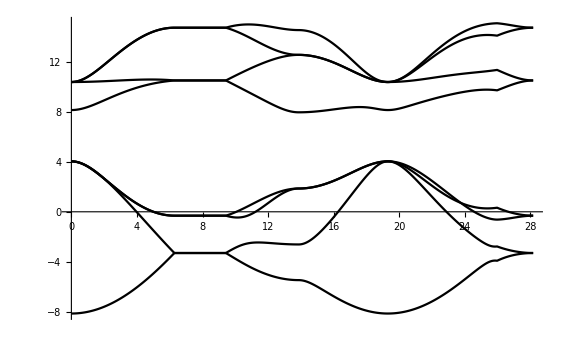

```mathematica
ClearAll["Global`*"]


H=ConstantArray[0.0,{8,8}];
emat=ConstantArray[0.0,{4,4}];
t=ConstantArray[0.0, {4,3}];

(* vectors to nearest neigbors *)
t⟦1⟧ = 0.25 * { 1,1,1 };
t⟦2⟧ = 0.25 * {1,-1,-1};
t⟦3⟧ = 0.25 * {-1,1,-1};
t⟦4⟧ = 0.25 * {-1,-1,1};

es=0.;ep=7.2; 
vss= -8.13/4.;
vspσ=-5.88 * √3./4. ;
vppπ=(3.17-7.51)/4.;
vppσ=(3.17+2.*7.51)/4.;
w=vppσ-vppπ;

emat⟦1,1⟧=es;
emat⟦2,2⟧=emat⟦3,3⟧=emat⟦4,4⟧=ep;

n=100;
path=ConstantArray[0.0,{6*n}];
bands=path;
pathdistance=path;

(*
FCC Symmetry Points;
--------------------;
Γ= 2π*{0.0,0.0,0.0};
W=2π*{0.5,0.0,1.0};
X=2π*{0.0,0.0,1.0};
L=2π*{0.5,0.5,0.5};
Κ=2π*{0.25,0.25,1};

Path;
Γ-X-W-L-Γ-Κ-X
*)

symmetrypoints = 2π*{{0.0,0.0,0.0},{0.0,0.0,1.0},{0.5,0.0,1.0},{0.5,0.5,0.5},{0.0,0.0,0.0},{0.25,0.25,1},{0.0,0.0,1.0}};
kdirections=ConstantArray[0.0,6];
Do[
(* Direction vectors to generate the path in k-space *)
kdirections⟦i⟧=1/n*(symmetrypoints⟦i+1⟧-symmetrypoints⟦i⟧)
,{i,Length[symmetrypoints]-1}]; 

Do[
(* path in k-space, each iteration assigns n elements of the path from one symmetry point to the next symmetry point *)
path⟦Range[(m-1)*n+1,m*n]⟧=ConstantArray[symmetrypoints⟦m⟧,n]+Table[kdirections⟦m⟧*l,{l,0.,n-1}]; 
,{m,6}]

Do[
(* total distance moved from the start till reaching each point k *)
pathdistance⟦i⟧=pathdistance⟦i-1⟧+Norm[path⟦i⟧-path⟦i-1⟧], 
{i,2,Length[pathdistance]}];

Do[
vmat=ConstantArray[0.0, {4,4}];
Do[

d=t⟦n⟧/Norm[t⟦n⟧]; (* direction cosines for a certain nearest neighbor *)
exp=ⅇ^(ⅈ*path⟦m⟧.t⟦n⟧);  (* bloch factor for the nth nearest neighbor *)

vmat⟦1,1⟧ += exp * vss;
vmat⟦1,2⟧ += exp * d⟦1⟧*vspσ;
vmat⟦1,3⟧ += exp * d⟦2⟧*vspσ;
vmat⟦1,4⟧ += exp * d⟦3⟧*vspσ;

vmat⟦2,1⟧ +=-exp * d⟦1⟧*vspσ;
vmat⟦2,2⟧ +=  exp * (d⟦1⟧^2*w+vppπ);
vmat⟦2,3⟧ +=  exp * d⟦1⟧*d⟦2⟧*w;
vmat⟦2,4⟧ +=  exp * d⟦1⟧*d⟦3⟧*w;

vmat⟦3,1⟧ +=-exp * d⟦2⟧*vspσ;
vmat⟦3,2⟧ +=  exp * d⟦2⟧*d⟦1⟧*w;
vmat⟦3,3⟧ +=  exp * (d⟦2⟧^2*w+vppπ);
vmat⟦3,4⟧ +=  exp * d⟦2⟧*d⟦3⟧*w;

vmat⟦4,1⟧ +=-exp * d⟦3⟧*vspσ;
vmat⟦4,2⟧ +=  exp * d⟦3⟧*d⟦1⟧*w;
vmat⟦4,3⟧ +=  exp * d⟦2⟧*d⟦3⟧*w;
vmat⟦4,4⟧ +=  exp * (d⟦3⟧^2*w+vppπ);

,{n,Length[t]}];

H⟦Range[4],Range[4]⟧=H⟦Range[5,8],Range[5,8]⟧=emat; (* Diagonal Blocks *)
H⟦Range[4],Range[5,8]⟧=vmat; (* Nearest neighbor interaction parts of the Hamiltonian *)
H⟦Range[5,8],Range[4]⟧=Transpose[vmat]*;

bands⟦m⟧=Sort[Eigenvalues[H]]
,{m,Length[path]}]

plot=ConstantArray[0,8];
Do[plot⟦j⟧=ListLinePlot[Table[{pathdistance⟦i⟧,bands⟦i,j⟧},{i,Length[pathdistance]}],PlotStyle->Black],{j,Length[plot]}];

Show[plot,PlotRange-> All]
```